```mathematica
ru = {1246491453600,3,1};
{n, k, r} = ru;
```

```mathematica
SetOptions[ArrayPlot, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

```mathematica
InitSearch[ru_,iwid_,max_:200,steps_:1000]:=
With[{fun=(If[#==0,-Infinity,max-#+1]&[LengthWhile[Reverse[CellularAutomaton[ru,{#,0},max]],Total[#]==0&]]&)},
{First[#],Length[#]}&/@SplitBy[
NestList[
With[{mm=MapAt[Mod[#+RandomInteger[{1,ru[[2]]-1}],ru[[2]]]&,#[[1]],RandomInteger[{1,iwid}]]},
With[{life=fun[mm]},If[life>=#[[2]],{mm,life},#]]]&,{#,fun[#]}&@CenterArray[{1},iwid],steps],Last]]
```

```mathematica
With[{ru={1246491453600,3,1}},SeedRandom[1246491777835];GraphicsRow[ArrayPlot[ArrayPad[#,1]&/@CellularAutomaton[ru,{#,0},115],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@#[[1,1]]&/@InitSearch[ru,10,200,4000]]]
```

```mathematica
%418[[All, 1]]
```

{{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,2,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,2,1,1,0,1,0,0,0,0,0,0}}

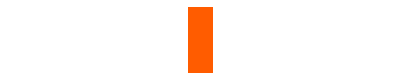
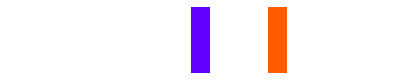
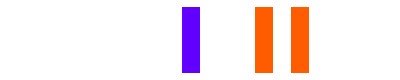
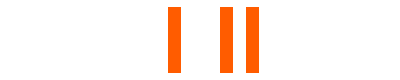
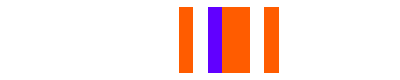

```mathematica
ArrayPlot/@List/@%418[[All, 1]]
```

```mathematica
InitSearch[{1246491453600,3,1},10,200,4000]
```

{{{{0,0,0,0,1,0,0,0,0,0},20},8},{{{0,0,0,0,1,0,0,0,2,0},30},1},{{{0,2,0,0,1,0,0,0,2,0},38},5},{{{0,2,0,0,2,0,0,0,2,0},48},2},{{{0,2,0,0,2,0,0,2,2,0},61},15},{{{0,2,0,0,2,1,0,2,2,0},80},1},{{{0,1,0,0,2,1,0,2,2,0},142},3969}}

```mathematica
%422[[All, 1, 1]]
```

{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,2,0},{0,2,0,0,1,0,0,0,2,0},{0,2,0,0,2,0,0,0,2,0},{0,2,0,0,2,0,0,2,2,0},{0,2,0,0,2,1,0,2,2,0},{0,1,0,0,2,1,0,2,2,0}}

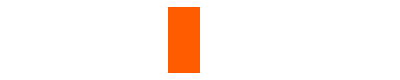
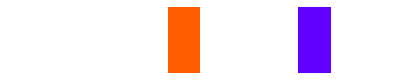
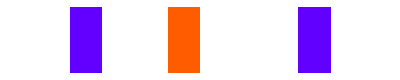
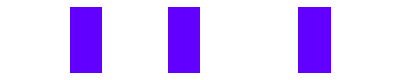
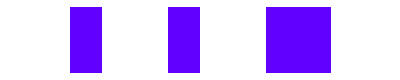
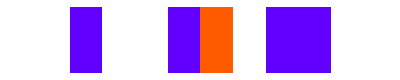
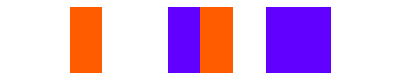

```mathematica
ArrayPlot/@ List/@ %422[[All, 1, 1]]
```

```mathematica
InitSearch[{1246491453600,3,1},10,200,4000]
```

{{{{0,0,0,0,1,0,0,0,0,0},20},2},{{{0,0,0,0,1,2,0,0,0,0},25},1},{{{0,0,0,0,1,2,0,0,0,1},29},1},{{{0,0,0,0,1,2,0,1,0,1},31},5},{{{0,0,0,0,0,2,0,1,0,1},32},3},{{{0,1,0,0,0,2,0,1,0,1},60},3},{{{0,1,0,0,0,2,0,2,0,1},89},3986}}

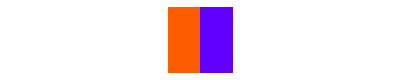
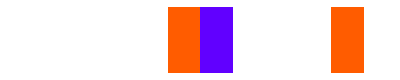
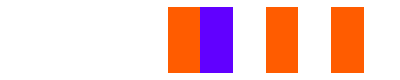
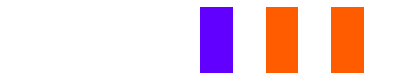
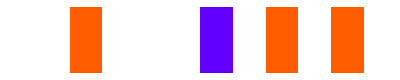
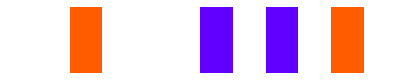
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@ List/@ %429[[All, 1, 1]]
```

```mathematica
list={1,2,3,4,5,6};
n=Length[list];
split={Take[#,⌈n/2⌉],Take[list,-⌊n/2⌋]}
```

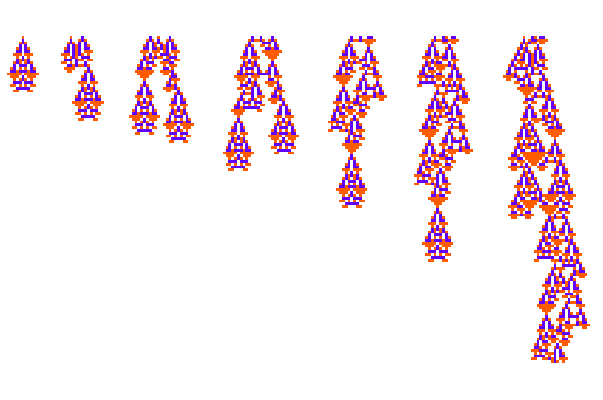

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#,1]&/@CellularAutomaton[ru,{#,0},115],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@#[[1,1]]&/@%422]
```

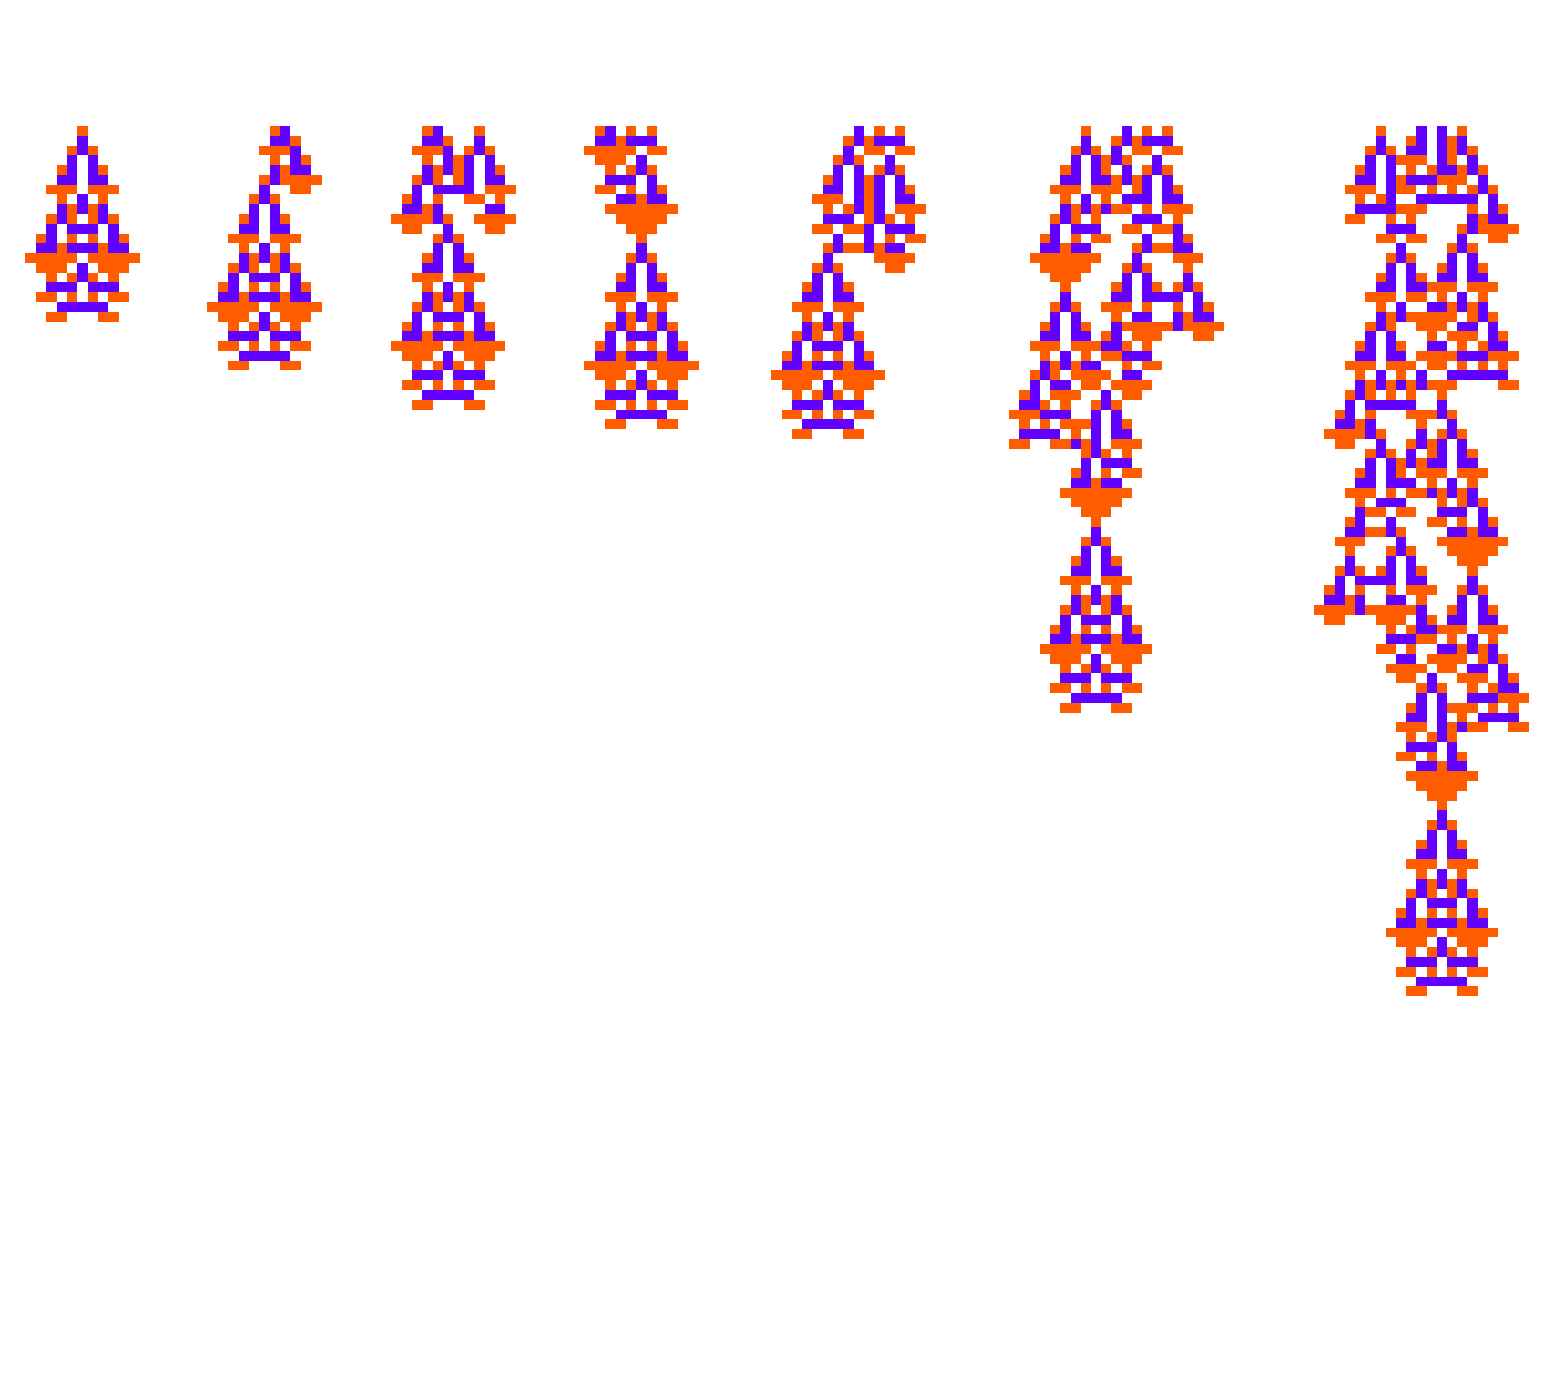

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#,1]&/@CellularAutomaton[ru,{#,0},115],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@#[[1,1]]&/@%429]
```

### Getting all possible combinations

```mathematica
a1 = InitSearch[{1246491453600,3,1},10,200,4000]
```

{{{{0,0,0,0,1,0,0,0,0,0},20},1},{{{2,0,0,0,1,0,0,0,0,0},30},1},{{{2,1,0,0,1,0,0,0,0,0},36},1},{{{2,1,0,0,2,0,0,0,0,0},38},1},{{{2,1,0,0,2,0,0,0,2,0},81},3997}}

```mathematica
a2 = InitSearch[{1246491453600,3,1},10,200,4000];
```

```mathematica
p1 = Table[{a1[[-1, 1, 1, ;;i]],a1[[-1, 1, 1, i+1;;]]},{i, Range[Length[a1[[-1, 1, 1]]] - 1]}];
p2 = Table[{a2[[-1, 1, 1, ;;i]],a2[[-1, 1, 1, i+1;;]]},{i, Range[Length[a2[[-1, 1, 1]]] - 1]}];
```

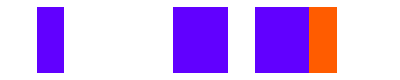
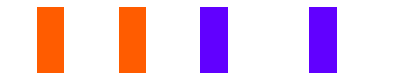
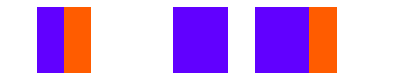
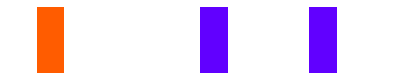
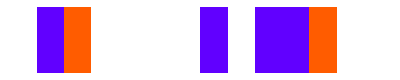
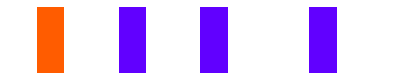
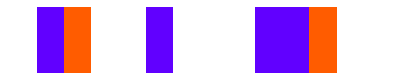
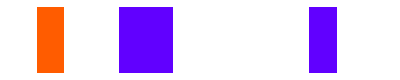
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot[List[#]]&, Table[{Join[p1[[i, 1]],{0, 0}, p2[[i, 2]]], Join[p2[[i, 1]],{0, 0}, p1[[i, 2]]]}, {i, Length[p1]}], {2}]
```

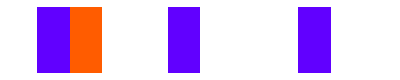
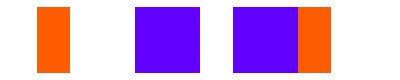

```mathematica
ArrayPlot/@List/@{a1[[-1, 1, 1]], a2[[-1, 1, 1]]}
```

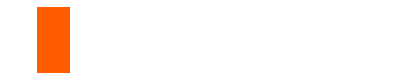
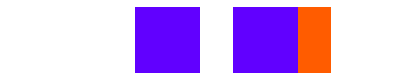
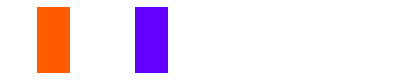
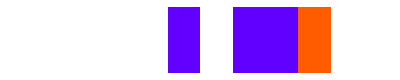
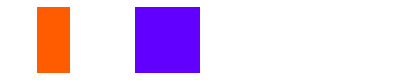
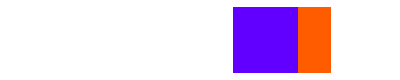
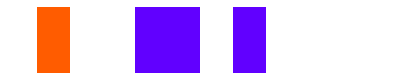
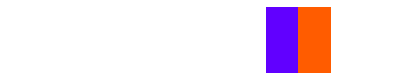
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot/@{List[PadRight[First[#],10 ]], List[PadLeft[Last[#], 10]]}&, p2]
```

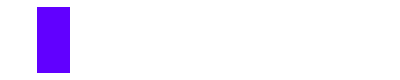
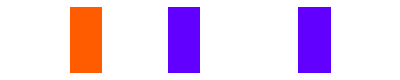
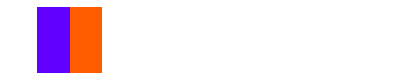
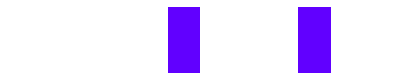
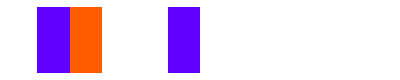
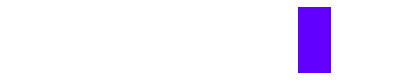
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot/@{List[PadRight[First[#],10 ]], List[PadLeft[Last[#], 10]]}&, p1]
```

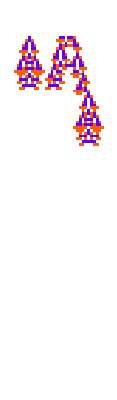
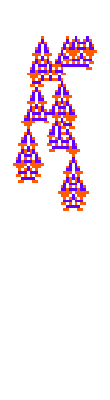
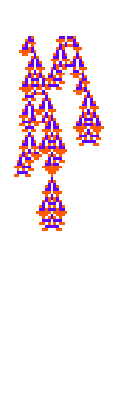
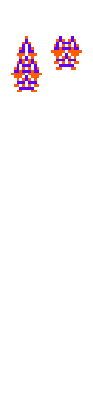
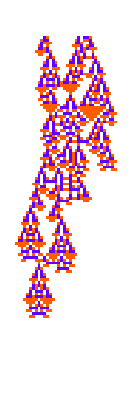
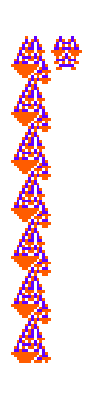
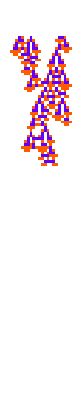
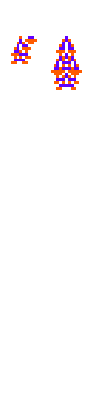
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot[ArrayPad[#,1]&/@CellularAutomaton[ru,{#,0},115],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&, Table[{Join[p1[[i, 1]],{0,0,  0, 0, 0, 0, 0, 0}, p2[[i, 2]]], Join[p2[[i, 1]],{0,0, 0, 0, 0, 0, 0, 0}, p1[[i, 2]]]}, {i, Length[p1]}], {2}]
```

### Min recomb evolution

```mathematica
RandomChoice[Delete[Range[0, k - 1], #+1]]&
```

```mathematica
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = MapAt[RandomChoice[Delete[Range[0, k - 1], #+1]]&, init, RandomInteger[{1, Length@init}]];
inits = Join@@@Permutations[Partition[newinit, UpTo[5]]];
newfitness = Min[TestCALifeTime[CellularAutomaton[ru, {#, 0}, {115, All}]]&/@ inits];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
{CenterArray[{1},20], 1}, 1000];
```

```mathematica
(*Join@@@*)Permutations[Partition[newinit, UpTo[5]]]
```

{{{1,0,0,0,1},{0,0,0,0,0}},{{0,0,0,0,0},{1,0,0,0,1}}}

```mathematica
CellularAutomaton[30, {{}}]
```

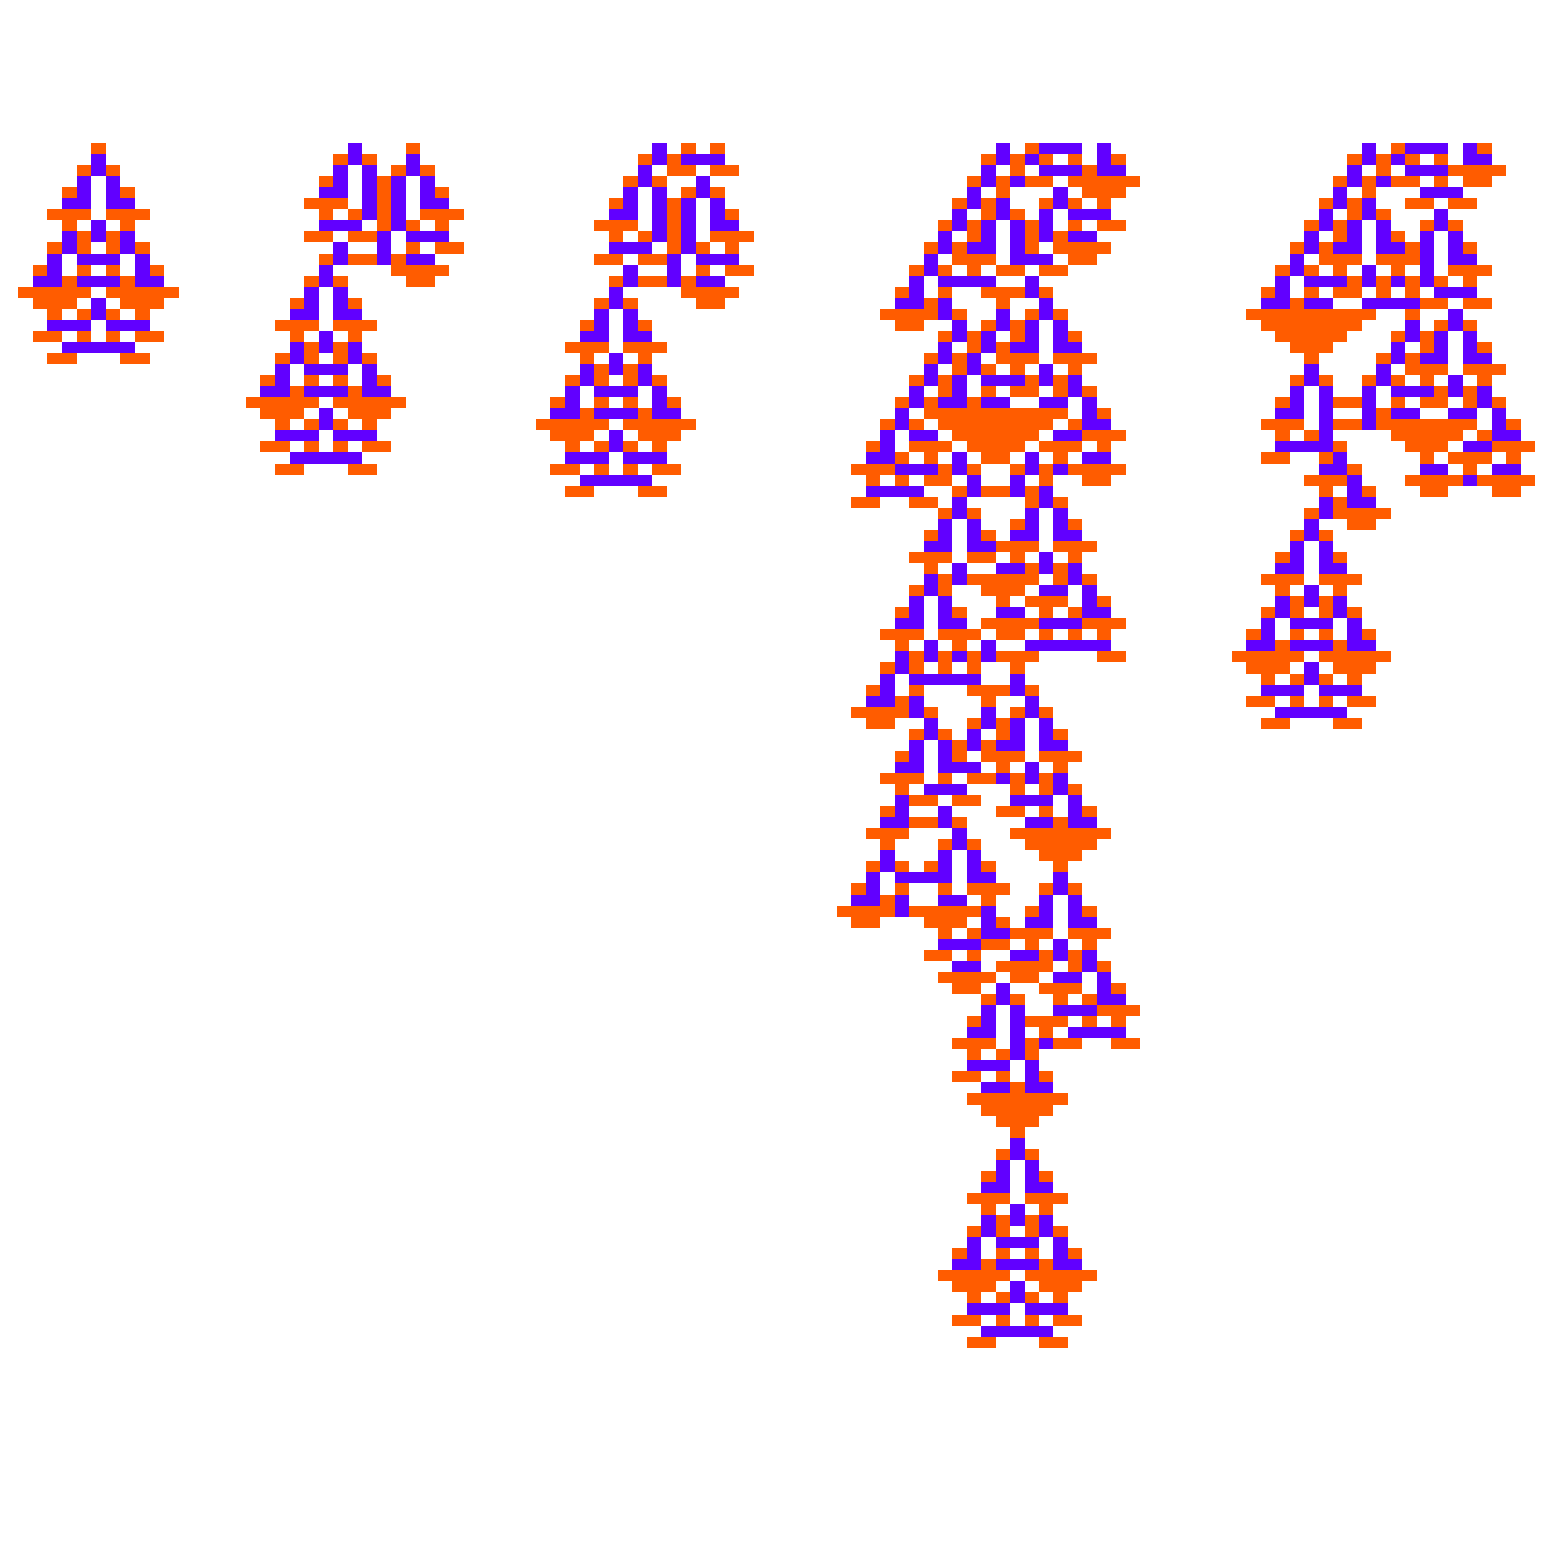

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{115, Automatic}]]&/@ GatherBy[shuffleevo, Last]]
```

```mathematica
Partition[#[[1, 1]], UpTo[5]]&/@ GatherBy[shuffleevo, Last]
```

{{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,1,2,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,2,1,2,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,2,1,2,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Length/@(Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last])
```

{4,4,12,12,4}

```mathematica
Length/@(Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last])
```

{4,4,12,12,4}

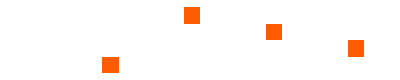
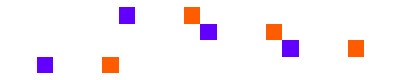
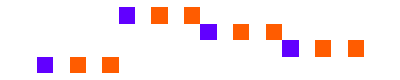
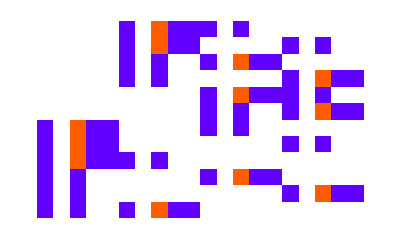
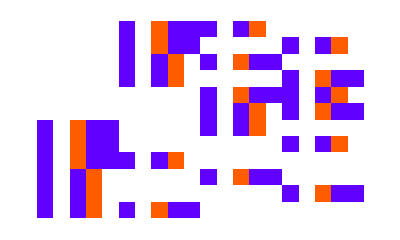

```mathematica
Map[ArrayPlot, Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last]]
```

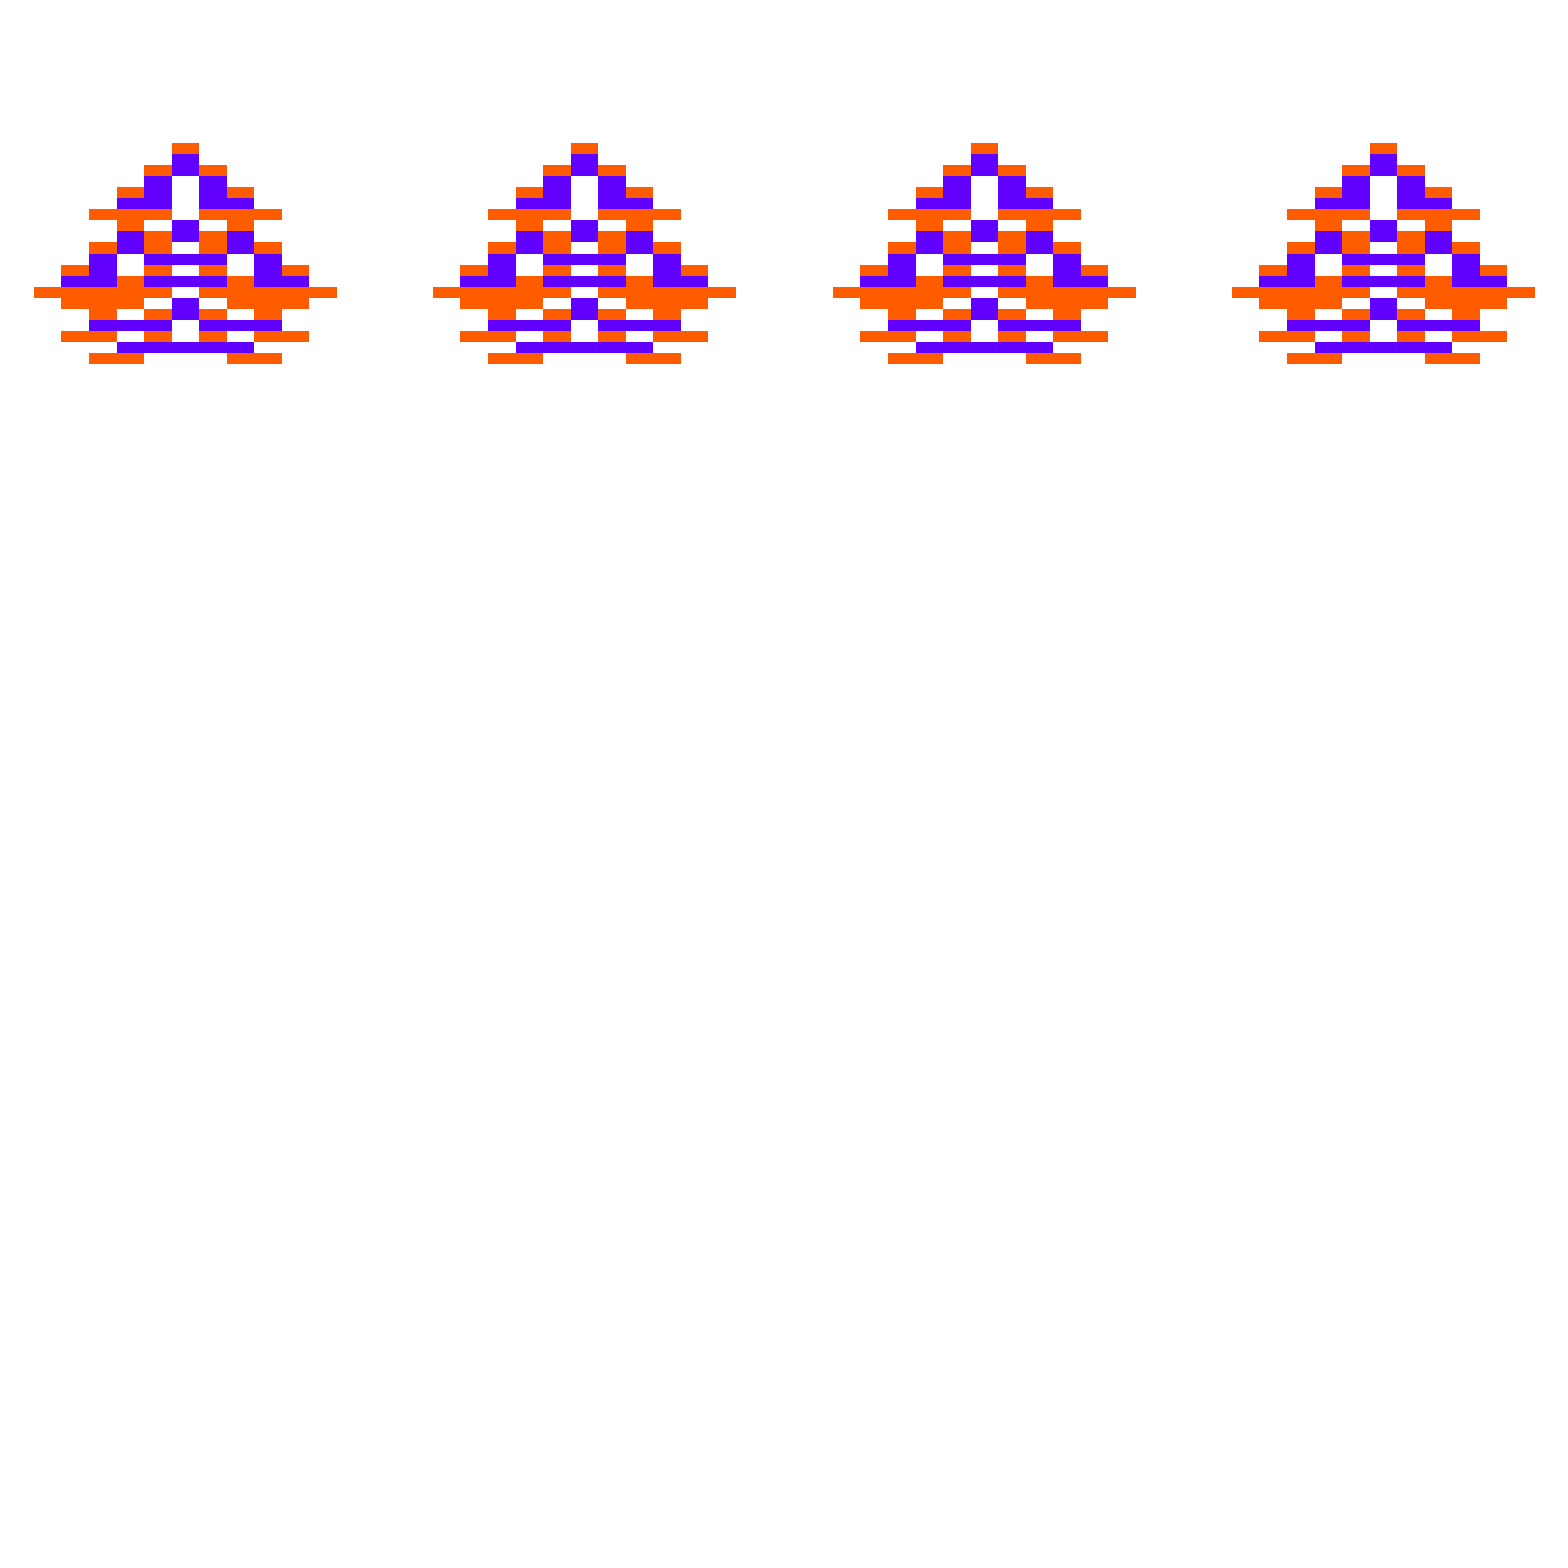
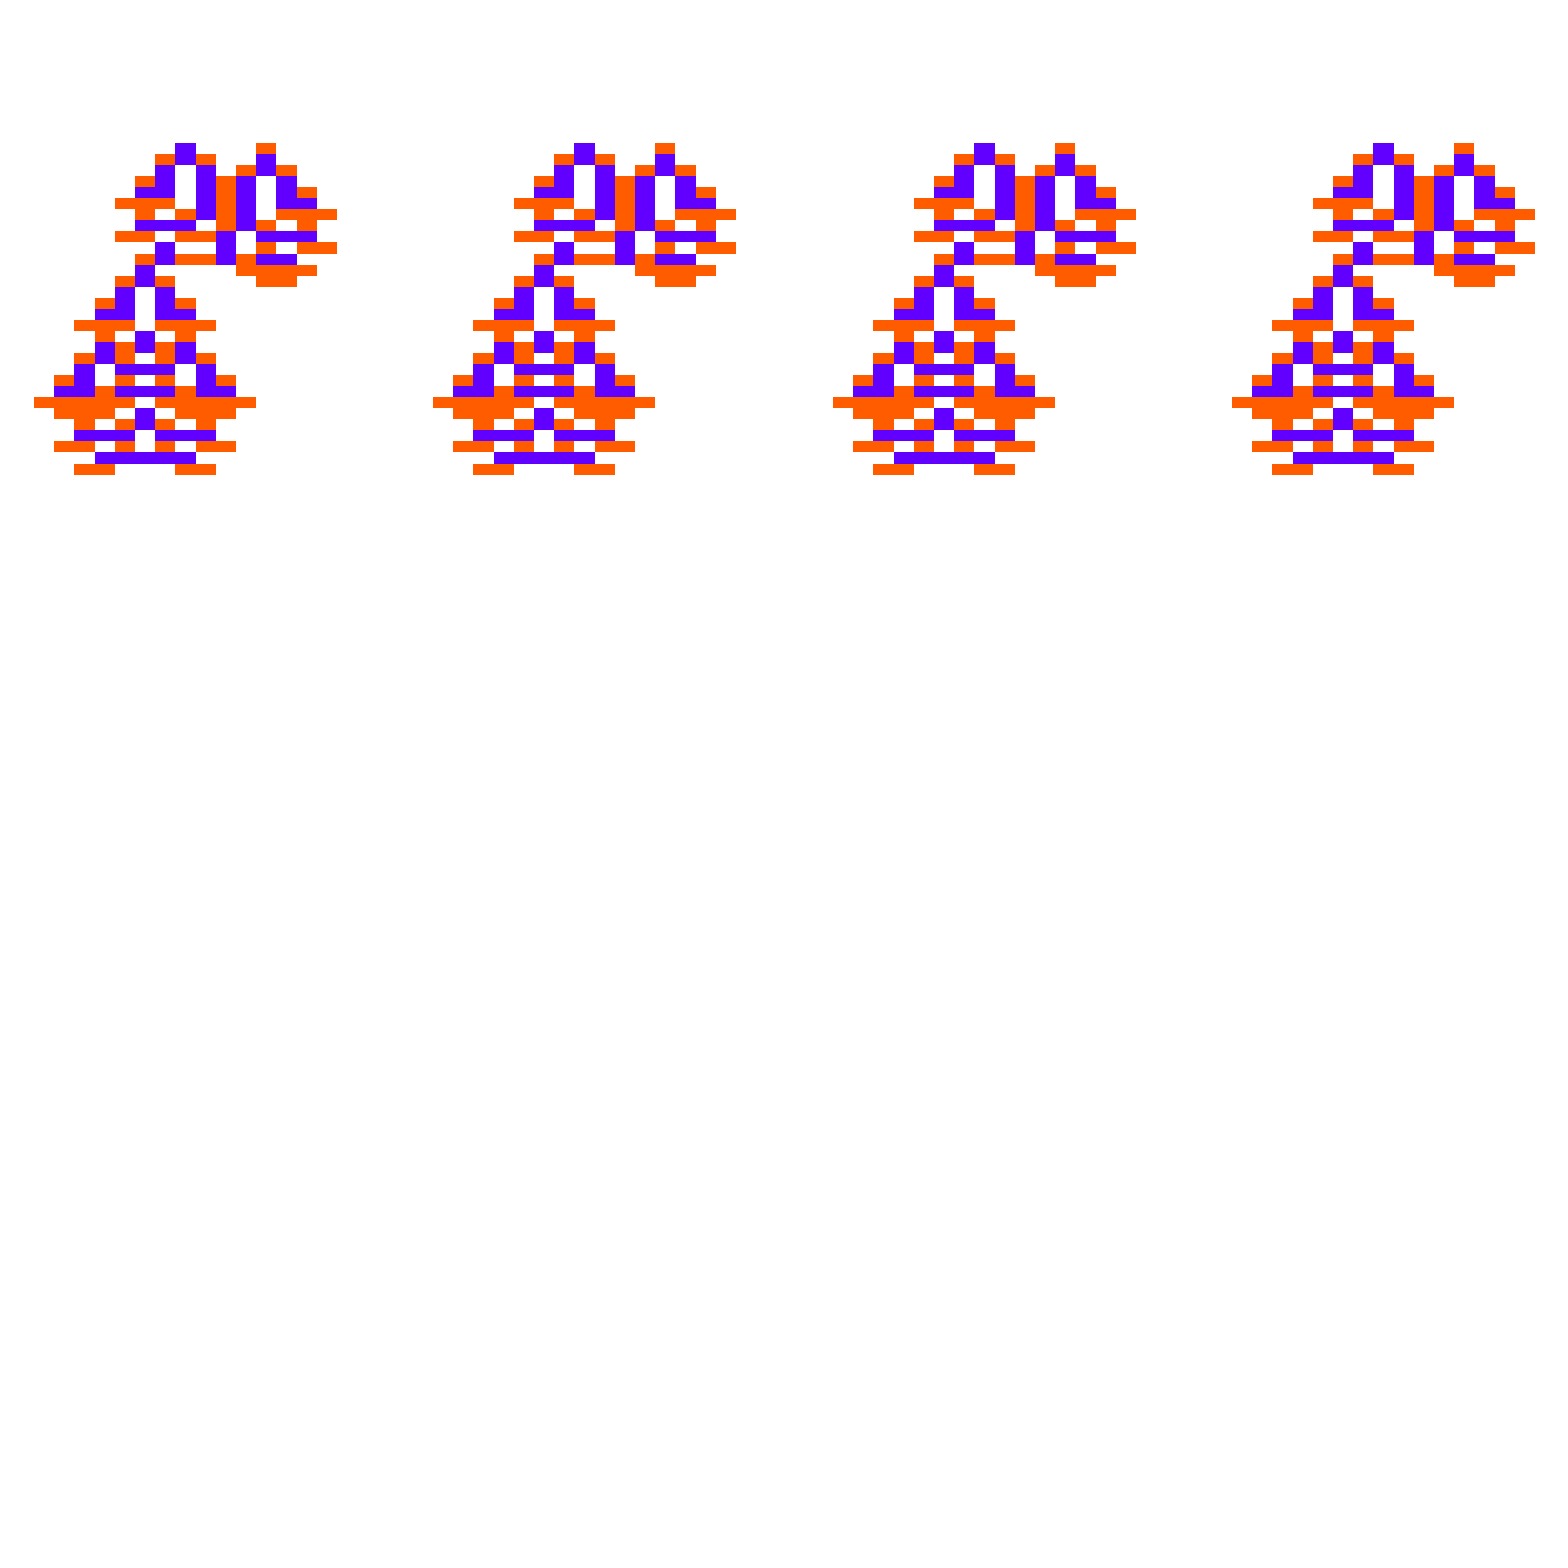
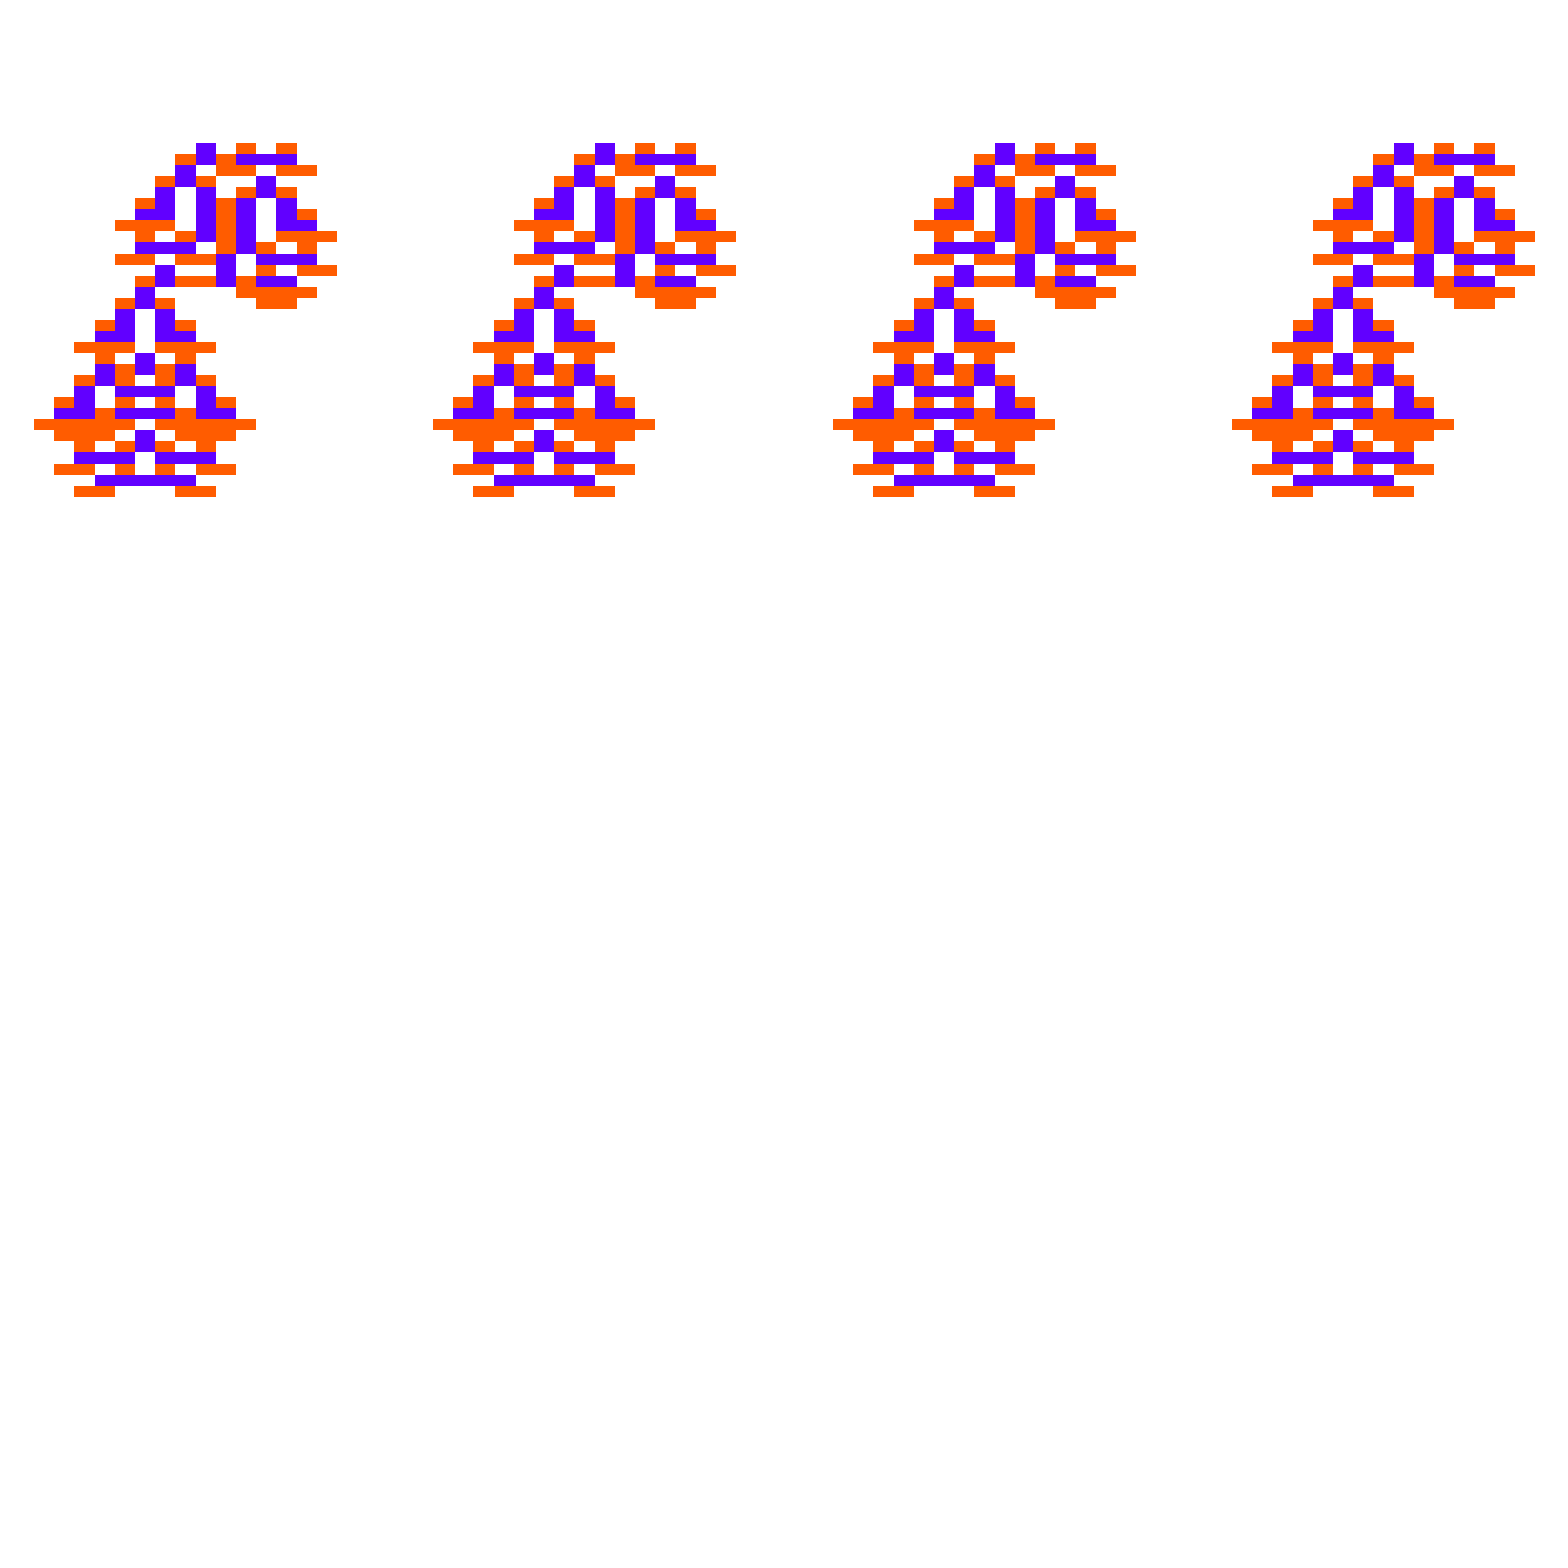
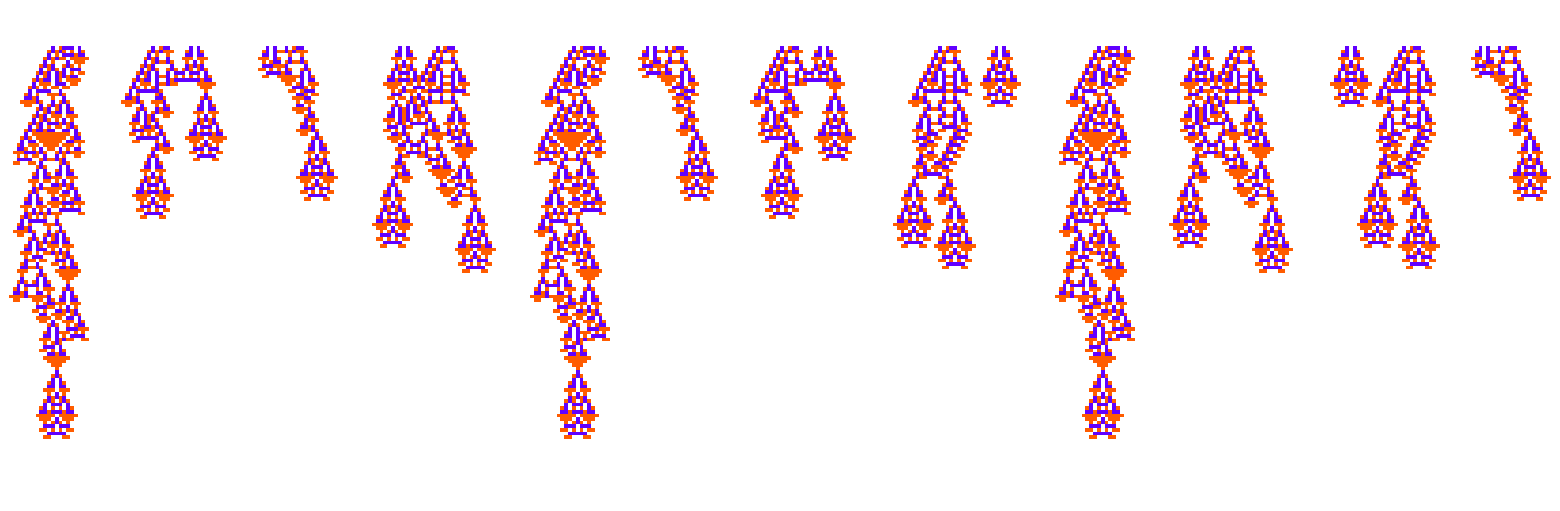
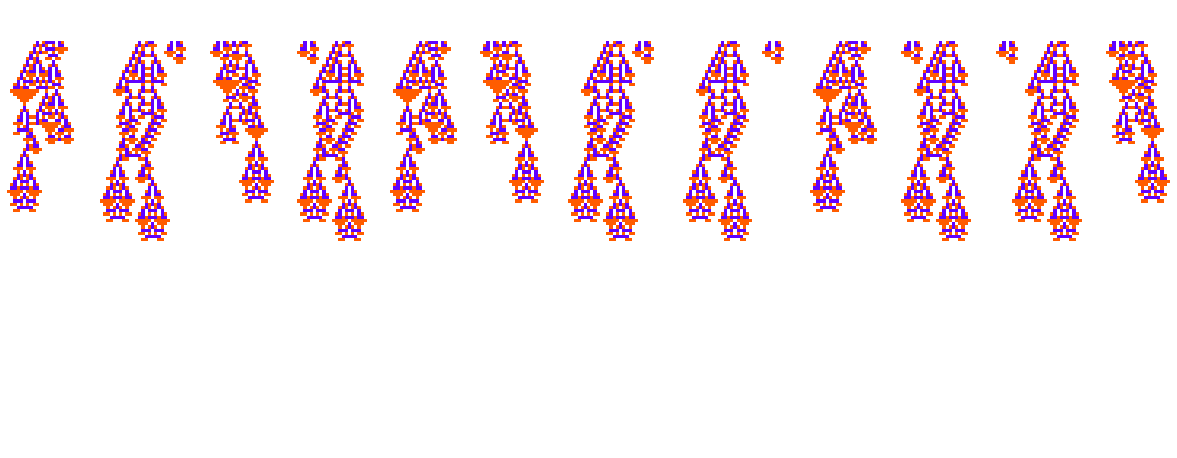

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#,0},{115, Automatic}]]&/@Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]]&/@ GatherBy[shuffleevo, Last]
```

### The transition from asexual to sexual evolution

Start with mutations and some recombination, then move just to recombination. May be that only recombination performs better.

#### Asexual with shuffling

```mathematica
SeedRandom[333890];
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = MapAt[RandomChoice[Delete[Range[0, k - 1], #+1]]&, init, RandomInteger[{1, Length@init}]];
inits = Join@@@Table[RandomSample[Partition[newinit, UpTo[5]]], 20];
newfitness = Min[TestCALifeTime[CellularAutomaton[ru, {#, 0}, {115, All}]]&/@ Prepend[inits, newinit]];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
{CenterArray[{1},50], 1}, 1000];
```

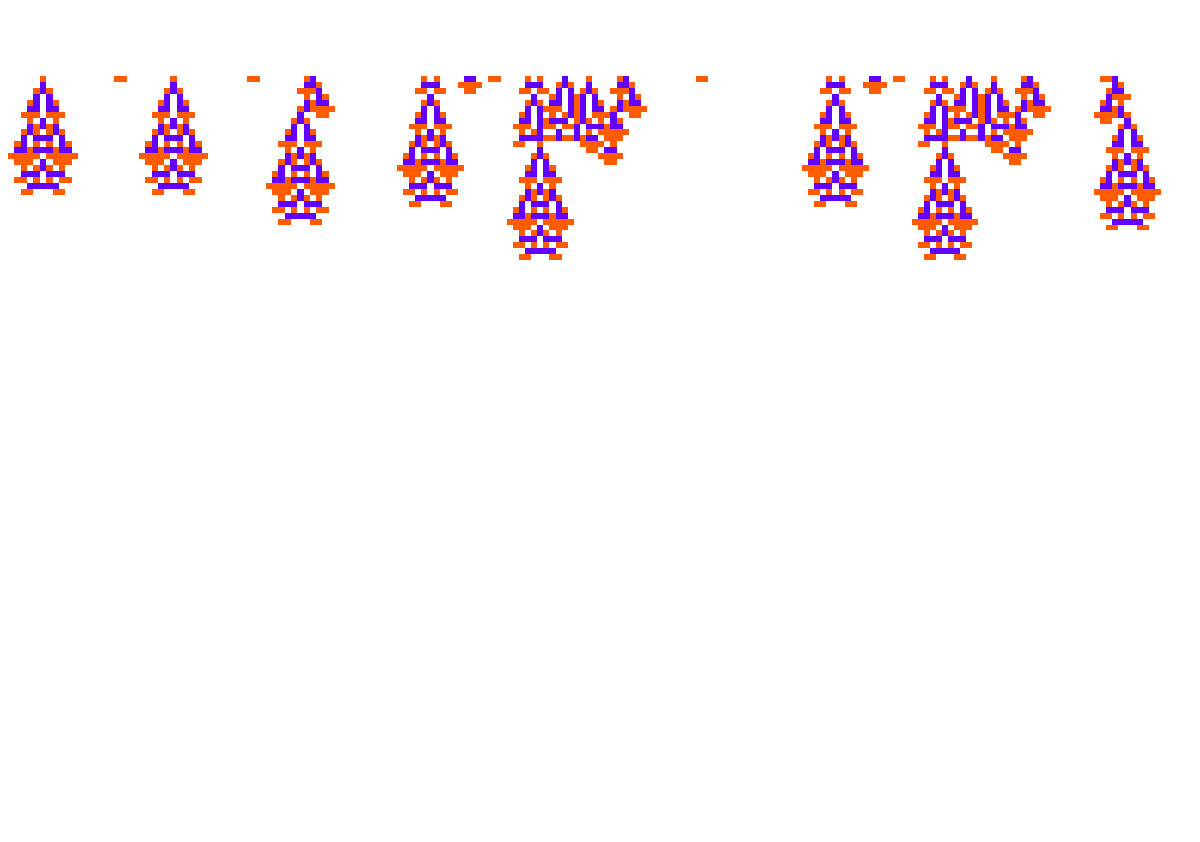

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{115, Automatic}]]&/@ GatherBy[shuffleevo, Last]]
```

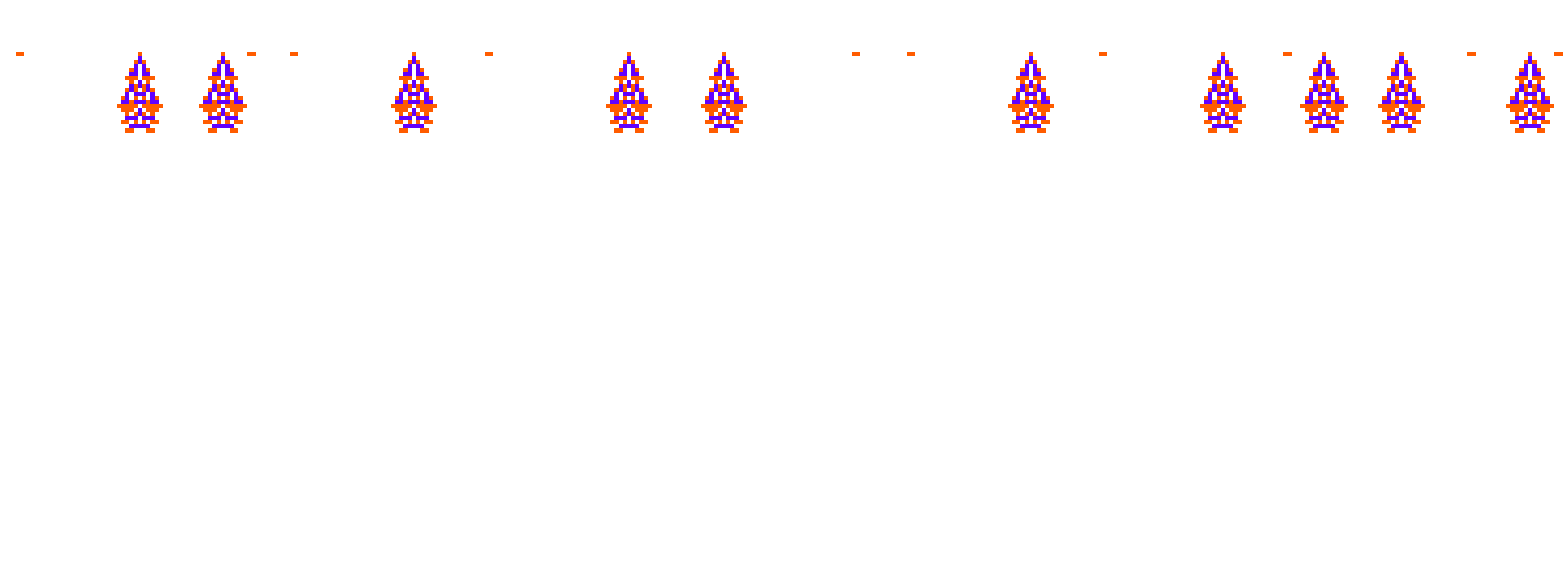
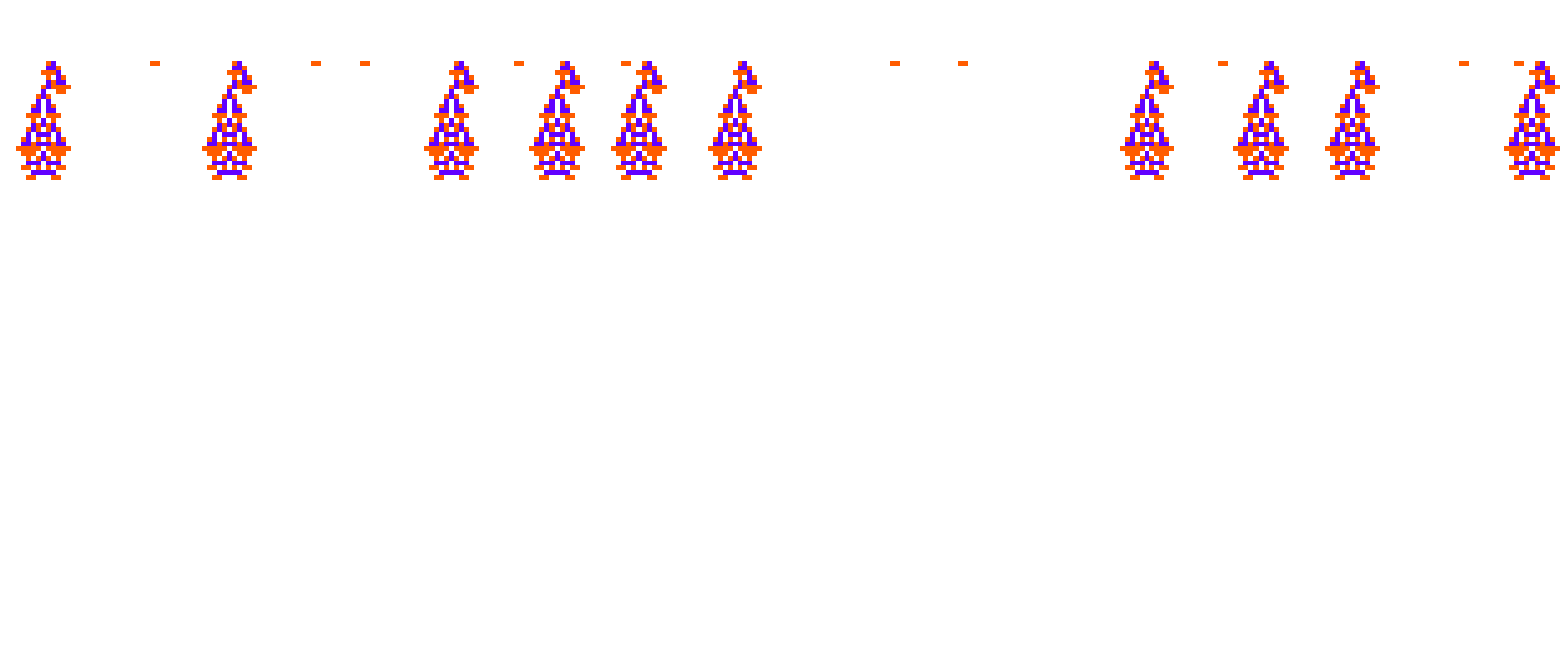
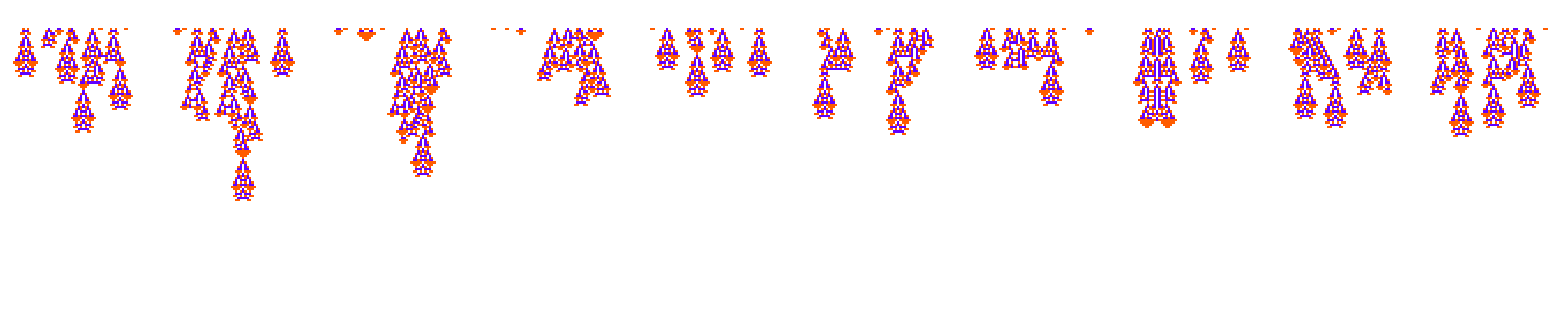
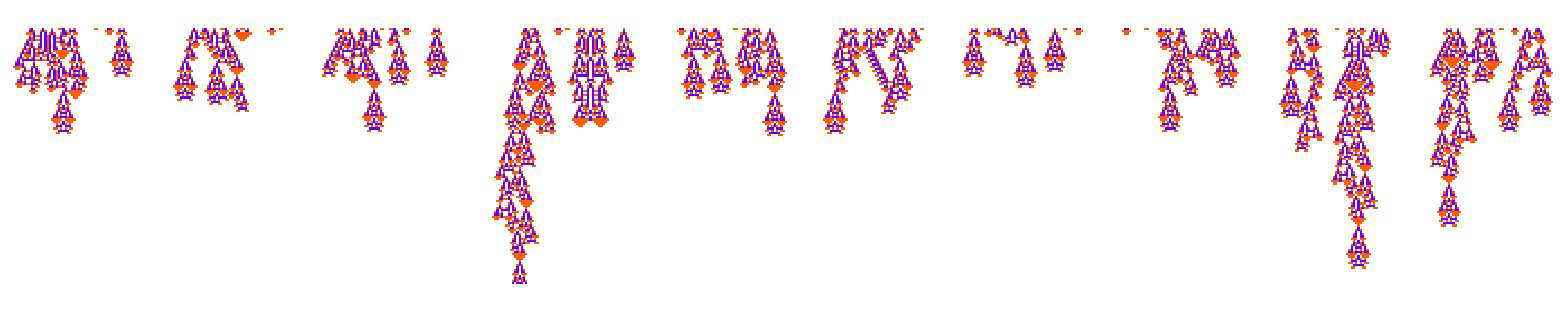
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#,0},{115, Automatic}]]&/@Join@@@Table[RandomSample[Partition[#[[1, 1]], UpTo[5]]], 10]]&/@ GatherBy[shuffleevo, Last]
```

```mathematica
shuffleevo[[-1, 1]] // Length
```

50

```mathematica
Permutations[Partition[shuffleevo[[-1, 1]], UpTo[5]]] // Length
```

1814400

```mathematica
shuffleevo[[-1, 1]]
```

{1,0,1,0,0,0,0,2,2,0,0,1,1,0,0,0,0,1,0,1,0,0,0,2,0,0,0,1,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,1,1,2,0,0}

#### Pure sexual now

```mathematica
astart = shuffleevo[[750]]
```

{{1,0,1,0,0,0,0,2,2,0,0,1,1,0,0,0,0,1,0,1,0,0,0,2,0,0,0,1,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,1,1,2,0,0},31}

```mathematica
SeedRandom[333893];
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = Join@@RandomSample[Partition[init, UpTo[5]]];
newfitness = Min[TestCALifeTime[CellularAutomaton[ru, {newinit, 0}, {300, All}]]];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
astart, 500];
```

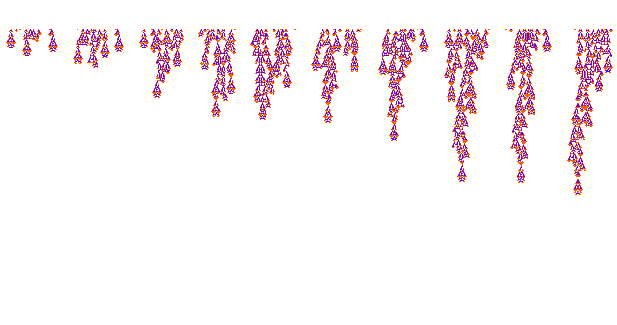

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{300, Automatic}]]&/@ GatherBy[shuffleevo, Last]]
```

#### Pure asexual now

```mathematica
SeedRandom[333891];
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = MapAt[RandomChoice[Delete[Range[0, k - 1], #+1]]&, init, RandomInteger[{1, Length@init}]];
newfitness = Min[TestCALifeTime[CellularAutomaton[ru, {newinit, 0}, {200, All}]]];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
astart, 500];
```

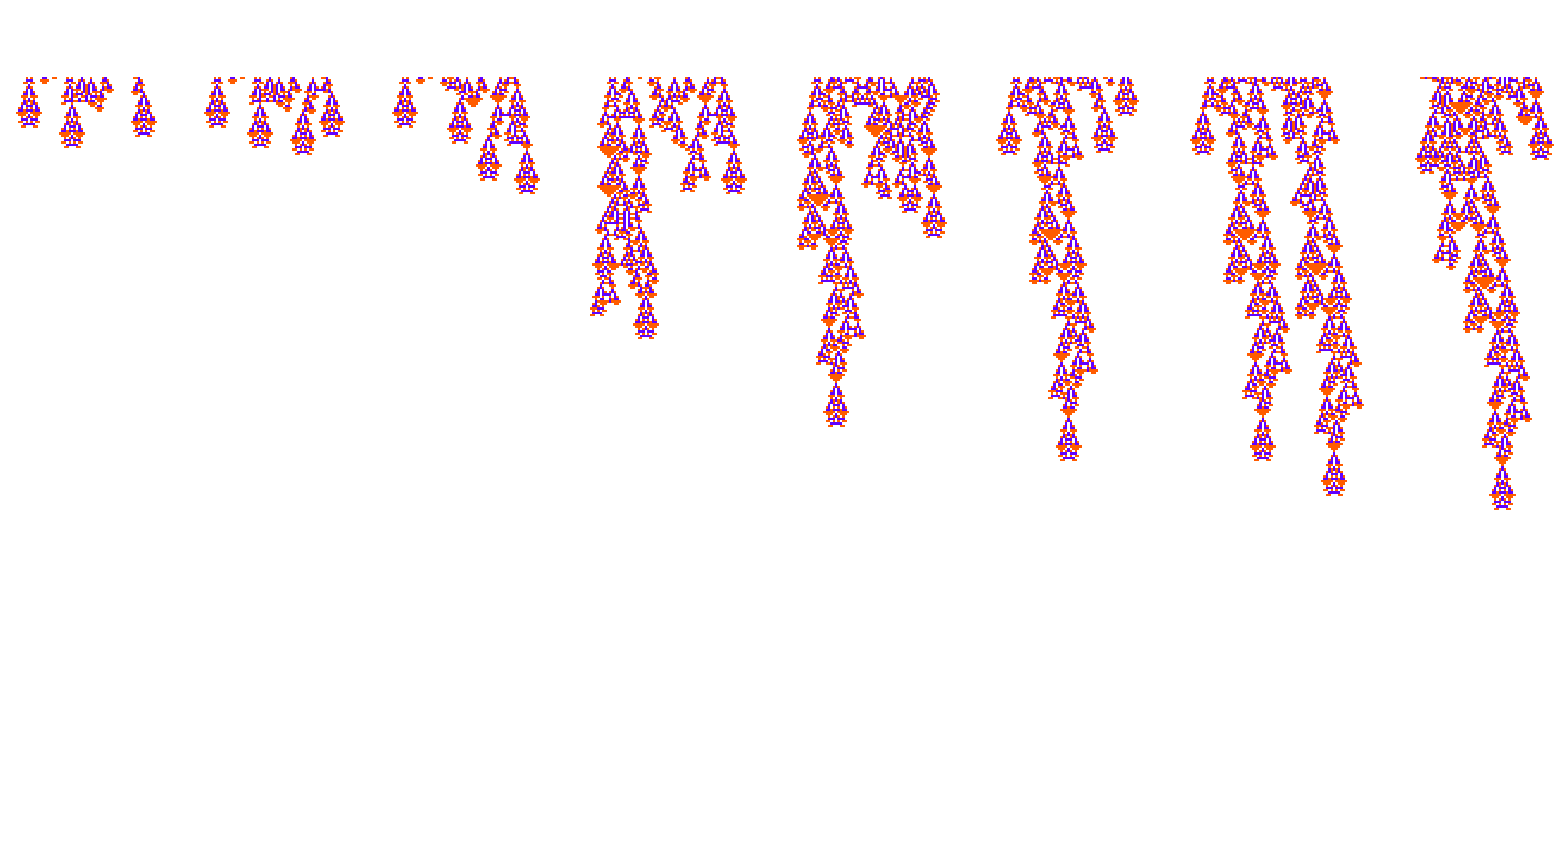

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{300, Automatic}]]&/@ GatherBy[shuffleevo, Last]]
```

### RandomSwap for more fair comparison

```mathematica
RandomSwap[list_, n_:1]:= 
Module[{idxs  = RandomSample[Range[Length[list]], 2]},
Nest[ReplacePart[#, {idxs[[1]]->list[[idxs[[2]]]], idxs[[2]]->list[[idxs[[1]]]]}]&, list, n]]
```

```mathematica
RandomSwap[{1, 2, 3, 4, 5, 6}]
```

{1,2,5,4,3,6}

### Hierarchy

Then try to add the ability for genes to dominate each other. So in the recombination process, the gene that lived longer in it’s section let’s say will win out or something like that.